# Lista 01 - Introdução à Física Computacional I

Lyliana Myllena Santos de Sousa - 11223740
Lyliana.sousa@usp.br

## Um oscilador harmônico simples consiste de uma massa 𝓂 e uma mola com constante elástica 𝓀. Em função do tempo 𝓉, ele se move em uma dimensão com posição 𝓍(t) e velocidade 𝓋(𝓉) dadas por: x(t) = A Cos[ωt + ϕ] e v(t) = - ω A Sin[ωt+ ϕ], com ω = √(k/m).

## 1.

Defina funções para 𝑥(𝑡) e 𝑣(𝑡), tratando as constantes como variáveis ainda não atribuídas;

```mathematica
ω = √(k/m);
x[t_]:= A*Cos[ω*t + ϕ]
v[t_]:= - ω*A*Sin[ω*t + ϕ]
```

## 2.

Trace gráficos separados de 𝓍(t) e 𝓋(t), para 0 ≤ t ≤ 10s , supondo 𝓂 - 1.75 Kg, 𝓀 = 2 N/m, A = 5m e ϕ = π/4.

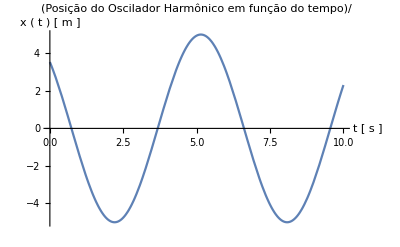

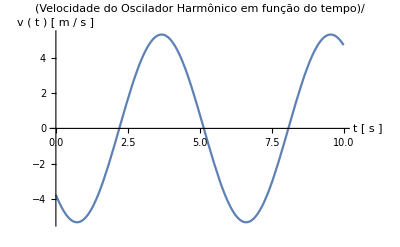

```mathematica
subs = {k-> 2, m -> 1.75, ϕ -> π/4, A -> 5};
Plot[x[t]/. subs, {t, 0 ,10},PlotLabel->"Posição do Oscilador Harmônico em função do tempo"/"",LabelStyle->{Black},AxesLabel->{HoldForm[t "["s"]"],HoldForm[x "("t")"   "["m"]"]}]
Plot[v[t]/. subs, {t, 0 ,10},PlotLabel->"Velocidade do Oscilador Harmônico em função do tempo"/"",LabelStyle->{Black},AxesLabel->{HoldForm[t "["s"]"],HoldForm[v "("t")"   "["m"/"s"]"]}]
```

## 3.

No instante inicial, 𝓉 = 0, a posição e a velocidade são dadas por x_0 = x (0) = A Cos[ϕ] e v_0 = v(0) = -ω A Sin[ϕ], de modo que: A = √(x_0^2 + v_0^2/ω^2) e ϕ = ArcTan(-v_0/(ω x_0)). Em seu código, defina 𝐴 e 𝜙 pelas equações acima. Trace os mesmos gráficos do item anterior, com os mesmos valores para 𝑚 e 𝑘, mas agora supondo 𝑥0=0.25m e 𝑣0=1.25m/s.

```mathematica
A = √(x0^2 + v0^2/ω^2);
ϕ= ArcTan[-v0/(ω *x0)];
```

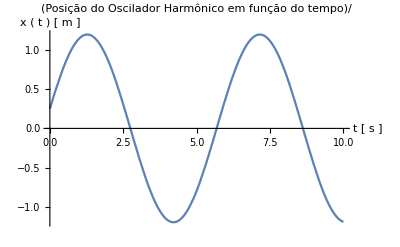

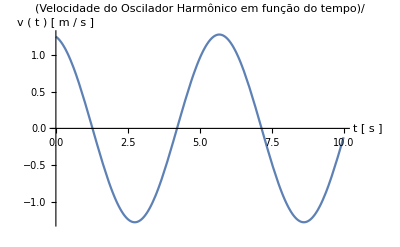

```mathematica
subs3 = {k-> 2, m -> 1.75, x0-> 0.25, v0 -> 1.25};
Plot[x[t]/. subs3, {t, 0 ,10},PlotLabel->"Posição do Oscilador Harmônico em função do tempo"/"",LabelStyle->{Black},AxesLabel->{HoldForm[t "["s"]"],HoldForm[x "("t")"   "["m"]"]}]
Plot[v[t]/. subs3, {t, 0 ,10},PlotLabel->"Velocidade do Oscilador Harmônico em função do tempo"/"",LabelStyle->{Black},AxesLabel->{HoldForm[t "["s"]"],HoldForm[v "("t")"   "["m"/"s"]"]}]
```

## 4.

A energia cinética de uma massa 𝓂 com velocidade 𝓋 é K = 1/2 mv^2. Para uma mola com deformação 𝓍 e constante elástica 𝓀, a energia potencial é U = 1/2 k x^2. Defina em seu código as funções K(𝓋) e U(𝓍) e trace gŕaficos dessas duas funções e de sua soma, todos em função do tempo e no mesmo conjunto de eixos, para 0 ≤ t ≤ 10s e utilizando os mesmos parâmetros do item anterior.

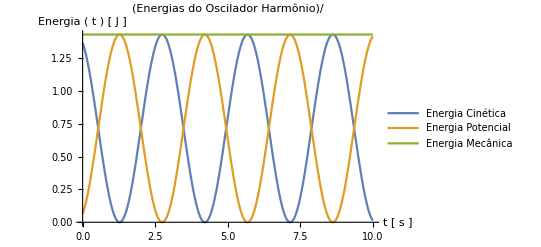

```mathematica
K[t_]:= 1/2 m*(v[t])^2
U[t_] :=  1/2 k*( x[t])^2
Etot[t_] := K[t] +U[t]
Plot[{K[t]/.subs3,U[t]/.subs3,Etot[t]/.subs3},{t,0,10}, PlotLabel->"Energias do Oscilador Harmônio"/"",LabelStyle->{Black},AxesLabel->{HoldForm[t "["s"]"],HoldForm[Energia "("t")"   "["J"]"]}, PlotLegends->{"Energia Cinética","Energia Potencial"," Energia Mecânica"}]
```